```mathematica
SetDirectory[NotebookDirectory[]];
```

# mu_scaling

## data

```mathematica
fpi=Flatten[Import["./LPA_muscaling_TCP/buffer/mSigma.dat"]];
mub=Flatten[Import["./LPA_muscaling_TCP/buffer/mub.dat"]];
mu=-(mub-mub[[1]])/mub[[1]];
data=Transpose[{Log[-mu[[2;;Length[mu]]]],Log[fpi[[2;;Length[mu]]]]}];
b1TCP=Transpose[{Log[-mu[[2;;Length[mu]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[mub]-2}]]}];

fpi=Flatten[Import["./LPA_muscaling_TCP_v2/buffer/mSigma.dat"]];
mub=Flatten[Import["./LPA_muscaling_TCP_v2/buffer/mub.dat"]];
mu=-(mub-mub[[1]])/mub[[1]];
data=Transpose[{Log[-mu[[2;;Length[mu]]]],Log[fpi[[2;;Length[mu]]]]}];
b1TCP2=Transpose[{Log[-mu[[2;;Length[mu]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[mub]-2}]]}];

fpi=Flatten[Import["./LPA_muscaling_TCP_v3/buffer/mSigma.dat"]];
mub=Flatten[Import["./LPA_muscaling_TCP_v3/buffer/mub.dat"]];
mu=-(mub-mub[[1]])/mub[[1]];
data=Transpose[{Log[-mu[[2;;Length[mu]]]],Log[fpi[[2;;Length[mu]]]]}];
b1TCP3=Transpose[{Log[-mu[[2;;Length[mu]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[mub]-2}]]}];

fpi=Flatten[Import["./LPA_muscaling_TCP_v4/buffer/mSigma.dat"]];
mub=Flatten[Import["./LPA_muscaling_TCP_v4/buffer/mub.dat"]];
mu=-(mub-mub[[1]])/mub[[1]];
data=Transpose[{Log[-mu[[2;;Length[mu]]]],Log[fpi[[2;;Length[mu]]]]}];
b1TCP4=Transpose[{Log[-mu[[2;;Length[mu]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[mub]-2}]]}];

fpi=Flatten[Import["./LPA_muscaling_TCP_v5/buffer/mSigma.dat"]];
mub=Flatten[Import["./LPA_muscaling_TCP_v5/buffer/mub.dat"]];
mu=-(mub-mub[[1]])/mub[[1]];
data=Transpose[{Log[-mu[[2;;Length[mu]]]],Log[fpi[[2;;Length[mu]]]]}];
b1TCP5=Transpose[{Log[-mu[[2;;Length[mu]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[mub]-2}]]}];

fpi=Flatten[Import["./LPA_muscaling_TCP_v6/buffer/mSigma.dat"]];
mub=Flatten[Import["./LPA_muscaling_TCP_v6/buffer/mub.dat"]];
mu=-(mub-mub[[1]])/mub[[1]];
data=Transpose[{Log[-mu[[2;;Length[mu]]]],Log[fpi[[2;;Length[mu]]]]}];
b1TCP6=Transpose[{Log[-mu[[2;;Length[mu]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[mub]-2}]]}];
```

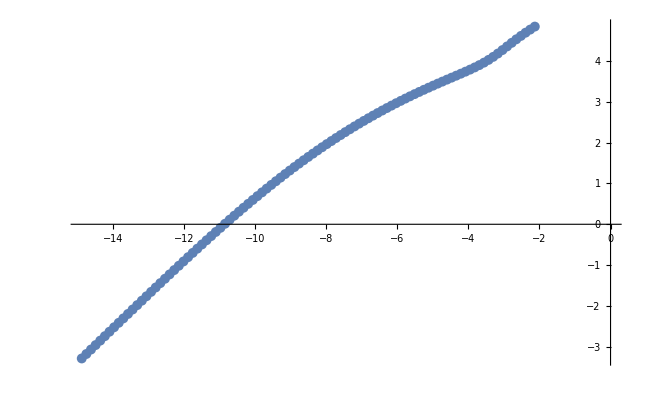

```mathematica
ListPlot[data]
```

## Plot

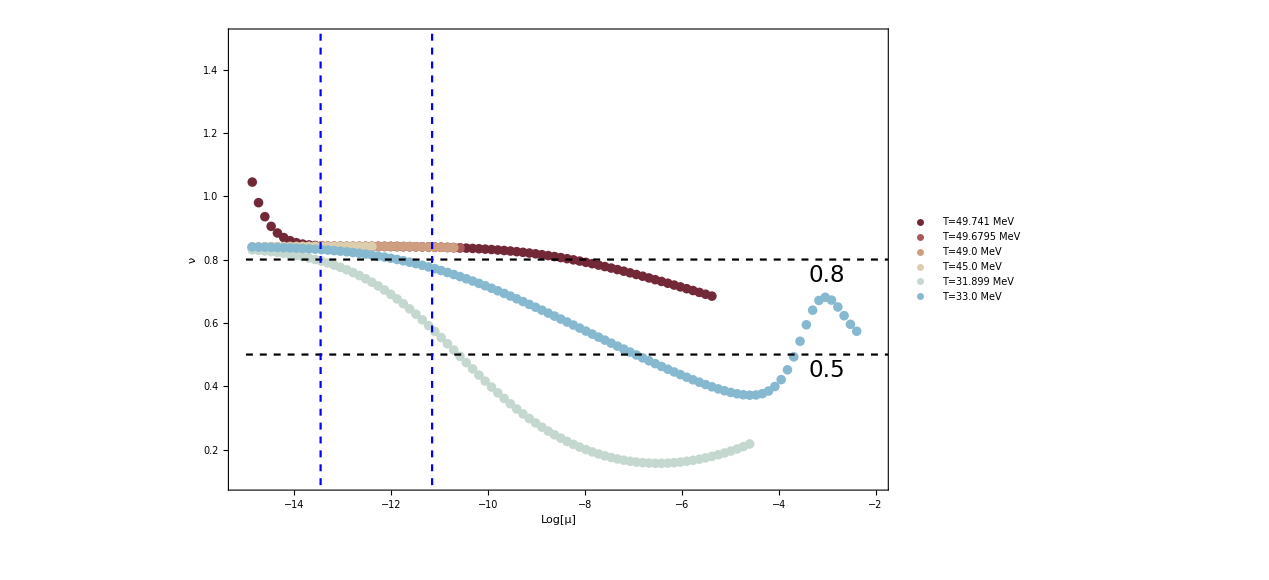

```mathematica
plotT=Show[ListPlot[{b1TCP,b1TCP2,b1TCP3,b1TCP4,b1TCP5,b1TCP6},
Frame->True,FrameLabel->{Style["Log[μ]",25,FontFamily->"Times",Black],Style["ν",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.15}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"T=49.741 MeV","T=49.6795 MeV","T=49.0 MeV","T=45.0 MeV","T=31.899 MeV","T=33.0 MeV"},LabelStyle->16],{0.5,0.75}],
PlotRange->{{-15.1,-2},{0.1,1.5}},AxesOrigin->{-15.1,0.1},FrameTicksStyle->Directive[15,Black]],
ListLinePlot[{{-15,0.8},{10,0.8}},PlotStyle->{Black,Dashed}],ListLinePlot[{{-15,0.5},{10,0.5}},PlotStyle->{Black,Dashed}],ListLinePlot[{{-13.4588,0.},{-13.4588,10}},PlotStyle->{Blue,Dashed}],ListLinePlot[{{-11.1563,0.},{-11.1563,10}},PlotStyle->{Blue,Dashed}],ImageSize->700,Background->None,Epilog->{Text[Style["0.8",23],{-3,0.75}],Text[Style["0.5",23],{-3,0.45}]}]
```

```mathematica
Export["./nu_v3.pdf",plotT]
```

./nu_v3.pdf